1

Introduction

## 1.1: Some Basic Mathematical Models; direction Fields

Differential equations:  equations involving derivatives.

Direction field: A plot that contains small arrow at every point and these arrows show the slope of the underlying function at every point.

Equilibrium solution:  A solution that shows the dependent variable staying constant at the independent one changing (often it is y held constant with a change in time). These are where the derivative of the dependent variable is 0 and the direction field will show horizontal lines as you move down the horizontal axis.

Steps to constructing a mathematical model

Identify the independent and dependent variables and assign letters to represent them. Often an independent variable is time.

Choose the units of measurement for each variable. Try to make them as convenient as possible.

Discover the basic underlying principle or law behind what you are trying to model.

Express the principle or law in terms of your variables chosen in step 1

Make sure that the units match up when you solve the equation

## 1.2: Solutions of Some Differential Equations

Initial condition: The value of all your Variables at a specific instance. Often this will be at t=0.

Initial Value Problem: The solving of a differential equation subject to initial conditions is called the  initial value problem and is abbreviated I.V.P.

General Solution: A that contains all possible solutions to a differential equation, subject on some values for arbitrary constants c_1...ect.

Integral Curves: The graphical representation of the general solution. This is simply a plot containing multiple lines, each defined by choosing a different value for your constants.

## 1.3: Classification of Differential Equations

Ordinary Differential equations (ODE’s): Are where your dependent variable only depends on one independent variable and there for you have only ordinary derivatives in your equation (no partials)

Partial differential equation (PDE’s): Differential equations where you have partial derivatives.

Order: The order of a differential equation is simply the same as the highest order derivative you have in the equation.

Linear ODE: A differential equation is linear if there are only linear terms in the equation. This one is a little fuzzy, but I know that if I see something like yy’ it isn’t linear. Also if you have a differential equation ∂y/∂t and somewhere you see the product of y and a different

2

First Order Differential Equations

## 2.1: Linear Equations; Method of Integrating Factors

There are various algorithms that will make the solving of first order linear differential equations much easier, but in order to apply them you need to express the equation in “standard form”:

ⅆy/ⅆt+p(t)*y  g(t).

In order to solve an equation in standard form we will often need to alter the equation by multiplying the entire thing by a integrating factor μ(t). We would like to choose μ(t) so that we end up getting the entire left side of the equation being the derivative of something.

We can find this integrating factor by following the steps below:

So we want ⅆy/ⅆt+p(t)*y   to be equal to d/dt[μ(t)*y]

We know from the chain rule that ⅆy/ⅆt+p(t)*y  = μ(t)dy/dt+(dμ(t))/dt y. Upon examination we can see that (dμ(t))/dt=p(t) *μ(t).

With some more algebra we get  (dμ(t)/dt)/(μ(t))=p(t) → d/dt[ln|μ(t)| = p(t) →

μ(t) = Exp[∫p(t) dt]

μ(t) dy/dt+μ(t)p(t)y=μ(t)g(t)

Using what we know about the integrating factor we have d/dt[μ(t)y]=μ(t)g(t)→ μ(t)y = ∫μ(t)g(t)dt→y = 1/(μ(t))∫μ(t)g(t) dt

y = 1/(μ(t))∫μ(t)g(t) dt

## 2.2: Separable Equations

Seperable: A differential equation is called separable if we can write it in the form M(x,y)+N(x,y)dy/dx=0  or M(x,y)dx+N(x,y)dy=0

If an equation is separable it also means that you will be able to isolate all the x terms from the y terms and then just integrate both side to find your solution.

It is really easy to solve separable equations if they are written in this form:

dy/dx = (f(x))/(g(y))→

g(y)dy = f(x)dx→

∫g(y)dy = ∫f(x)dx →

y = f(x) + constants

## 2.3: Modeling with First Order Equations

Steps to modeling with first order equations

Generate a model using the steps from section 1.1

Analysis of the model: this is where you are actually presented with the problem of solving the differential equation.

Compare results with experimental results or observation: After you have found mathematical solutions to your model you need to test the validity of your model and make sure that it holds up.

### Example: The Tank Problem

A lot of problems in first order linear differential equations involve a reservoir of some type with a rate of inflow to the reservoir and a rate of outflow out of the reservoir.

This is an example problem and the steps to solving it: At time t = 0 a tank contains Q_0 lb of salt dissolved in 100 gal of water. Assume that water containing 1/4 lb of salt/gal is entering the tank at a rate of r gam/min and that he well-mixed solution is draining at the same rate. Write a model that will help you determine the amount of salt Q(t) at any moment in time.

dQ/dt = rate in - rate out = r/4-(r*Q)/100, Q(0)=Q_0

This is a linear equation and can therefore be solved using the method of an integrating factor where μ(t) = e^(rt/100).

Q(t)  = e^(-rt/100)*∫e^(rt/100)*r/4 dt=25 + ce^(-rt/100)

It can be verified that using the initial condition you get c = Q_0-25

This makes the solution to the IVP Q(t) = 25+ (Q_0-25)e^(-rt/100)

## 2.4: Differences Between Linear and Non-Linear Equations

THEOREM 2.4.1: If the functions p and g are continuous on an open interval I:α<t<β containing the point t = t_o, then there exists a unique function y = ϕ(t) that satisfies the differential equation y’ + p(t)y = g(t) for each t in I.

THEOREM 2.4.2: Let the functions f and ∂f/∂y be continuous in some rectangle α < t < β, γ < y < δ containing the point (t_0,y_0). Then in some interval t_o-h < t < t_0 + h contained in α < t < β, there is a unique solution y = ϕ(t) of the initial value problem y’ =  f(y,t), y(0) =t_0.

Sometimes you will not be able to do an integral or have some other obstacle that prevents you from solving for y directly. That is ok . Go as far as you can and when you are done simplifying you will get what is called the implicit solution. The explicit solution is preferable and is in the form y = f(t)

### Summary of properties of Linear differential Equations of the form y’ + p(t)y = g(t)

On the interval where the Coefficient functions p(t) and g(t) are continuous there is a solution contain a constant c that is  the general solution to the differential equation.

There is an explicit solution to the differential equation.

The points of discontinuity can be seen before solving the problem by looking at possible points of discontinuity in the coefficient functions p(t) and g(t).

## 2.5: Autonomous Equations and Population Dynamics

Atonomous Equation: A differential equation.08 in which the independent variable doesn't appear explicit in the original differential equation, thus it has form dy/dt = f(y). (in this case the independent variable is t and its only appearance is in the derivative term)

These types of equations are common in economics and population growth studies.

For graphically understanding the behavior of the solutions without solving the equation we have a few tools:

Because these equations are written at dy/dt = f(y) it is helpful to draw a plot of f(y) vs y. The first step in doing this is to find the critical points  or roots (zeros) of f(y). We can then choose values in between critical points and see if the curve comes from above or below to meet the critical point on the horizontal (y in this case) axis. If it comes from above we will be able to know that the solutions are increasing on the interval between the critical points and if it comes from below we know that they are decreasing. (We usually draw lines on the axis to show direction so if the it is above the y line we draw an arrow on the axis to the right and it is below we draw a line to the left on the axis..)

The phase line is just a vertical line representing the y axis where the arrows we hinted at above are shown.  This will allow us to determine the characteristics of the equilibrium

Solutions identified from our plot of f(y) and y. There are three possibilities and they are summarized as follows: One arrow in and one out | Both out | Both in
semi-stable | unstable | Asomptotically Stable

Finally we can plot some sample solutions of our equation on a graph of y vs. t. We start by drawing horizontal lines at all of our Equilibrium solutions and then using the phase line to determine whether the in between starting points head to a particular critical point or away from them. We determine changes in concavity of our solution line by looking at the second derivative of y. This is also the first derivative of f(y) because of how the differential equation is written. On our graph of f(y) vs y we will see these changes in concavity as points of inflection (change from heading up to down).

Example dy/dt = y^3-2 y^2-3y→ y(y-3)(y+1), zeros are -1,0,3

```mathematica
Plot[y^3-2y^2-3y,{y,-2,5}];
Solve[D[y^3-2y^2-3y,y]==0,y]//N
```

{{y→-0.535184},{y→1.86852}}

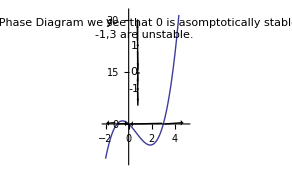
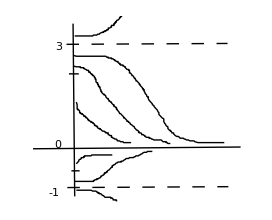

### Types of Autonomous equations and their solutions

#### Exponential growth or decay:

dy/dt = ry and y(0) = y_0, where r is the rate of growth or decay.

This is a separable equation and we get dy/y= r dt → ∫1/y dy = ∫r dt → ln[y] = rt +c→y = ce^rt→ y = y_0 e^rt

These types of solutions aren’t always realistic because they imply that there is room for y to grow very quickly as t increases without ever hitting a ceiling of sorts.

#### Logistic Growth or decay: Similar to the exponential, but they account for the fact that the growth rate actually depends on the current value of the population.

dy/dt = h(y)y

We want h(y) to be about equal to r when y is small and we want it to decrease as y gets bugger so the best way to do that is to say that h(y) = r-ay where r is the growth rate in the absence of limiting factor and a is a positive constant

dy/dt = (r-ay)y→ dy/dt = r(1-y/K) where K = r/a

We want to look for equilibrium or constant solutions, those are where there is no change or dy/dt =0, this can be written r(1-y/K)y = 0. They are also known as critical points.

In this case K is called the carrying capacity or the saturation level. It is actually an equilibrium solution to the differential equation.

You will probably have to do partial fractions here, but the solution works out to be:

y = (K y_0)/(y_0 + (K - y_0)e^-rt)

#### Logistic Growth with a Thresh hold: Combines the ideas from both of them to say you have a threshold like before, but that you also have a factor that makes dy/dt negative when y is large so it decreases down to the threshold, rather than just increasing.

dy/dt=-r (1-y/T)(1-y/K)y There will be three circuital points, y=0,T,K

The solution to this equation will depend on the actual problem, but it is in form.

## 2.6: Exact Equations and Integrating Factors

Exact Equation: An Equation is said to be exact if it can be written in the form M(x,y) + N(x,y) y’ =0 Where (∂M)/(∂y)=(∂N)/(∂x).

We don't know how to solve these all the time so we need to learn a new trick. Let's say that (∂ψ)/(∂x)=M(x,y) and (∂ψ)/(∂y)= N(x,y)

If that is the case M(x,y) + N(x,y) y’ = d/dx ψ{x,ϕ(x)]=0

We now have a two step problem to finding out what ψ is:

We know that ψ_x=m→ψ=∫M dx +g(y) //in this case the constant of integration is a function of the other variable in our integrand. That is noted as g(y) [we also know that ψ_y=N]

We write that in the middle  and expand in this way d/dyψ = ∫M dx + g(y)=ψ_y=N(x,y). We should see that everything with an x is canceling in the ψ part except g’(y) and we will get that is either equal to a constant (sometimes 0) or a function of only y. We then integrate that and get g(y)

With g(y) we go back to ψ = ∫mdx + g(y) = c and that is our solution.

If M_y≠N_x there might exist an integrating factor μ such that (μM)_y=(μN)_x→ μ_y M + μM_y = μ_x N + μN_x (* this is by the product rule  *)

For this class we will assume that μ is either only a function of x or only a function of y.

If we asume that μ is only a function of x we know that μ_y=0 and we can solve for μ and show that μ(x) = Exp[∫(M_y-N_x)/N dx]

By the same logic μ as a function of y can be found t o be μ(y) = Exp[∫(N_x-M_y)/M dy]

After that we multiplly everything through by μ and solve for ψ using the algorithm above.

## Review types of equations and their solutions

### Linear First order equations

dy/dt+p(t)y = g(t)

μ(t) = Exp[∫p(t) dt]

y = 1/(μ(t))[∫μ(t)g(t)dt +c]

### Separable First order equations

M(x,y) dx + N(x,y)dy = 0 or M(x,y)+N(x,y)dy/dx=0 or the most useful dy/dx=(f(x))/(g(y))

g(y)dy = f(x)dx

∫g(y)dy = ∫f(x)dx +c→ algebra gets you y = f(x)

### Autonomous Equations (population dynamics)

dy/dt = f(y) (* t doesn’t appear explicit in our differential equation)

Get an idea of what it looks like by plotting f(y) vs y, the phase line, and some sample solutions (name critical points as semi-stable, unstable, or asymptotically stable*)

#### Exponential Growth or Decay

dy/dt = ry and y(0) = y_0, where r is the rate of growth or decay.

This is a separable equation and we get dy/y= r dt → ∫1/y dy = ∫r dt → ln[y] = rt +c→y = ce^rt→ y = y_0 e^rt

y = y_0 e^rt

#### Logistic Growth or Decay

dy/dt = h(y)y = r(1-y/K), K = r/a, a is positive constant

Carrying capacity is K

y = (K y_0)/(y_0 + (K - y_0)e^-rt)

#### Logistic Growth with a Threshold

dy/dt=-r (1-y/T)(1-y/K)y

Critical points are y = 0, y = T, y = K

Solve probably using Partial Fraction Integration

### Exact Equations

M(x,y)dx + N(x,y)dy = 0 or M(x,y) + N(x,y) dy/dx=0

Check to see if M_y=N_x (subscripts mean partial derivatives). If so the equation is exact. If not see below for help to find integrating factor

(∂ψ)/(∂x)=M(x,y) and (∂ψ)/(∂y)= N(x,y)

ψ = ∫ M dx + g(y)

d/dy[∫M dx + g(y)] = ψ_y=  N // all x’s should drop out when you equate ψ_y=N. If not you did it wrong. This lets you integrate to solve for g(y). You have to integrate because in doing the derivative of the ∫  you get a g’(y).

The solution is ∫M(x,y) dx + g(y) = c

Finding an Integrating Factor (* note that for this class our integrating factors will always be functions of only one vairable *)

If we want an integrating factor as a function of x, μ(x) = Exp[∫(M_x-N_y)/N dx]. We will be able to tell before we do the integration if this is what we want because all the y’s will have to drop out of the (M_x-N_y)/N in order to get a function of only x out of the integral.

If we want an integrating factor as a function of y, μ(y) = Exp∫(N_y-M_x)/M dy] We will be able to tell before we do the integration if this is what we want because all the x’s will have to drop out of the (N_y-M_x)/M in order to get a function of only x out of the integral.

3

Second Order Differential Equations

## 3.1: Homogenous Equations with Constant Coefficients

A second order differential equation has the forom (d^2 y)/dt^2= f(t,y,dy/dt) where f is just some function.

This is linear if the equation has the form:

f(t,y,dy/dt) = g(t) - p(t) dy/dt - q(t)y, which is usually expressed in this form:

y'' + p(t)y' + q(t) y = g(t)

If a second order ODE cannot be expressed in either of these ways then it is said to be non-linear.

2nd order equations will involve two integrations and will therefore need 2 initial conditions to solve for the two constants.

Homogeneous:  A 2nd order linear ODE is homogeneous if g(t)=0. If not then it is said to be non-homogeneous.

In the case of a homogeneous eqution where the coeffcients are constants you can write it in this form:

ay''+by'+cy =0, leading to this characteristic equation

ar^2+br+c=0

Characteristic Equation:  The characteristic equation for a 2nd order linear ODE with constant coefficients is written in the form of equation (3.4). It is significant becuase if you find the roots, r, to this equation y = e^rtis a solution to the differential equation.

### Two real, distinct roots to the characteristic equation

If you have two, real, distinct roots to the characteristic equation, the general solution to the ODE is given by:

y = c_1 e^(r_1 t)+c_2 e^(r_2 t)

## 3.2: Solutions of Linear Homogeneous Equations; the Wronkskian

We will now extend the ideas from the previous section, but before doing so we introduce operator notation. We say that L[y](t) = y’’+p(t)y’+q(t)y

Theorem 3.2.1 (existence and Uniqueness Theorem): If you have the initial value problem y’’+P(t)y’+q(t)y=0, y(t_0)=y_1, y'(t_0) = y'_0, where p - q- g are all continuous on an open interval I, then you have only one solution y = ϕ(t) that exists in the interval I( that is to say ϕ(t) is the general solution).

This Theorem says three important things:

The IVP has a solution; that is the solution exists

The IVP has only one solution; tha tis the solution is unique

The solution ϕ is defined throughout the interval I and is at least twice differentiable there.

Theorem 3.2.3: Suppose that y_1 and y_2 are solutions to L[y]=0 and that initial condistions are given. Then it is always possible to chose constants c_1 and c_2 so that y = c_1 y_1+c_2 y_2 satisfies the IVP if and only if the wronkskian W = |(y_(t_0) | y_2(t_0)
y'_1(t_0) | y'_2(t_0))| is not exactly zero at t_0.

W(y_1,y_2)(t_0) = |y_(t_0) | y_2(t_0)
y'_1(t_0) | y'_2(t_0)|

This theorem says that if you can find any point t_0 on the interval I where W ≠ 0 y_1 and y_2 constitute a fundamental set to that differential equation.

A note is that if you have any point t_0 where W ≠ 0, then all points on I have W≠ 0. The opposite is also true. If W = 0 for some point t_0 on I, W =0 for all points in the interval I.

Theorem 3.2.: (Abel’s Theorem): If y_1 and y_2 are solutions to L[y]=0, then the Wroknskian W(y_1,y_2)(t_0) = c*Exp[-∫p(t)dt]

W(y_1,y_2)(t_0) = |y_(t_0) | y_2(t_0)
y'_1(t_0) | y'_2(t_0)| = c Exp[ -∫p(t) dt ]

This therem tells us that in order to compute the wronksian we don’t have to solve for y_1 and y_2, we  simply need to look at p(t) and use this equation. That is a powerful analytical tool that tells us whether we need to spend the time solving an equation or not.

## 3.3: Complex Roots of the Characteristic equation

If you are given a 2nd order linear homogeneous ODE with constant coefficients it will have a characteristic equation ar^2+br+c =0. If, when solving for the roots you have a negative discriminant (b^2-4ac) the roots will be complex conjugates of one another. The general form for this situation is shown below

r = (-b ± √(b^2-4ac))/(2a), b^2-4ac<0

r_1 = -b/(2a)+(√(b^2-4ac))/(2a), r_2= -b/(2a)-(√(b^2-4ac))/(2a)

r_1 = λ+i μ, r_2 = λ- i μ where λ = -b/(2a) and μ = (√(4ac-b^2))/(2a)

So, if these are your roots and you know that y = e^rt you can say that y = e^(t (λ±μ i)), which can be simplified down this general solution form:

y = c_1 e^λt Cos[μ t] + c_2 e^λt Sin[μ t]

## 3.4: Repeated Roots; Reduction of Order

We have so far discussed two of the three possibilities for the roots of the characteristic equation. The third and final possibility is that you have a real root that is repeated.

In order to solve equations of this type we will have to use a method called reduction of order. We will develop this method in this section.

First, we need to understand that this happens when the discriminant = b^2-4ac =0. In this case r_1=r_2=-b/(2a)-> y_1 = e^(-b t/2a).

To find a second solution to this equation we will say that y_2 = v(t) y_1(t), or that it is just a function of t times the first solution.

The following is the proof of the solution:

0 = y''+p(t)y'+q(t)y
= v'' y_1+2v'y_1'+vy''+p(t)[v' y_1+vy'_1]+q(t)vy_1
= v'' y_1+2v' y_1+p(t)v' y_1+v[y_1''+p(t)y_1'+q(t)y_1]
= v'' y_1+2v' y_1+p(t)v' y_1
= v'' y_1+[2y_1'+p(t)y_1]v'=0

Now the question is what should we pick for v(t). Well the easiest thing to do is just say that v(t) =t and the general soution becomes:

y = c_1 e^(r_1 t)+c_2 t e^(r_2 t)

## 3.5: Nonhomogeneous Equations; Method of Undetermined Coefficients

### General Theory about non-homogeneous equations

We now turn to and discuss the possibilities where g(t) ≠0. We have a few theorems that can help us out.

Theorem 3.5.1: If y_1 and y_2are two solutions of the nonhomogeneous equation  L[y]=g(t), bhen their differece ( y_1-y_2)  is a soltion to the corresponding homogeneous equation L[y]=0.

Theorem 3.5.2: The general solution of the nonhomogeneous equation L[y]=g(t) can be written in the form y = ϕ(t) = c_1 y_1+c_2 y_2 + Y(t) where the y’s are a fundamental set to the corresponding homogeneous equation, the c’s are arbitrary constants, and Y is some specific solution to the non homogeneous equation.

To summarize the effect of the last two theorems, we will list 3 steps to solving a nonhomogeneous 2nd order linear ODE:

Find the general solution c_1 y_1+c_2 y_2to the corresponding homogeneous equation.

Find a single particular solution to the non-homogeneous case.

Add these two together to get the general solution to the nonhomogeneous.

### The Method of undermined coefficients

The method of undetermined coefficients involves looking at the function g(t) and making an educated guess about what the form of the particular solution needs to look like. This will be a general guess with coefficients that will need to be solved for by taking appropriate derivatives and plugging the results in for y’’, y’, and y in the initial equation L[y]. Doing so will give us a system of linear equations we can use to solve for any coeffcients we need.

We will discuss using this process to find solutions to equations where g(t) is either an exponential, polynomial, or sin-cos or sums and products of those three. Below is the form of the particular solution for all the cases we have talked about.

g(t) | Y_p(t)
P_n(t) = a_0 t^n+a_1 t^(n-1)+...+a_n | t^s(At^n+Bt^(n-1)+...+A_n)
P_n(t)e^αt | t^s e^αt(At^n+Bt^(n-1)+...+A_n)
p_n(t)e^αt Sin[βt] | t^s e^αt{Cos[βt](At^n+Bt^(n-1)+...+A_n)+Sin[βt](At^n+Bt^(n-1)+...+A_n)}

In the table above t^srefers to the smallest degree of t that will insure that no part of Y_pis already contained in y_h. Sometimes you don’t have one of the components and in that case you just substitute 1 in for them in that case.

This method is self correcting in that if you don’t include enough in your guess you will not be able to solve for coefficients without some kind of contradiction (like A =1 and A=0 from two equations). If you assume too much you will simply get that some of the coefficients =0 .

Make sure you don’t forget to include the sum of Sin + Cos if g(t) has EITHER sin or cos in it and you have y’ somewhere. This is because in taking one derivative you introduce the other type of term and make it so you would not be able to solve the equaiton. If you only see y and y’’ you are safe to use just the type that appears in g(t), however including both in this situation will just lead to one of the coefficients=0 which is a way to make sure you don’t go wrong.

## 3.6: Variation of Parameters

There are more methods than just undertermined coefficients for solving the non-homogeneous case. We will discuss another right here and it is called “variation of parameters”.

This way is more general than undertermined coefficients because it doesn’t require any specific guesses about the form of Y_p. The drawback, however, is that this method does require the evaluation of some integrals that can get pretty ugly.

The theory behind this method is to find the homogeneous case again, y_h = c_1 y_1+c_2 y_2 and then relplace c_1 = u_1(t), c_2 = u_2(t) so you have y_p = u_(1(t))y_1+u_2(t)y_2. The next step is to take the neccesary derivatives and substitute y_p,(y')_p, and (y'')_p in to the initial ODE. I am not going to include the proof/derivation of this method here. This can be seen at the following 6.

The result of this function is that a particular solution to L[y]=g(t) is given by:

Y_p(t) = ∑_(m=1)^n y_m(t)∫(g(t)W_m(t))/(W(t))dt =-y_1∫(g(t)y_2)/(W(t))dt+y_2∫(g(t)y_1)/(W(t))dt for 2nd order equations

In the equation above y_m(t) is simply the mth equation in the general solution to the corresponding homogeneous solution. W(t) is the wronkskian of those solutions at t and W_m(t) is computed by finding teh wronkskian of the matrix determined by replacing the mth column of the vector with [0 | 0 | ... | (1])^T.

## 3.7: Mechanical and Electrical Vibrations

2nd order linear ODE’s with constant coefficients are super common in the study of many physical systems. Among the simplist and most common are mechanical and electrical vibrations like masses on springs, oscillating pendulums, flow of electric current in a simple series circuit.

We will use the example of a mass on a spring to derive the mathematical concepts behind such systems.

### Mass on a spring

In this case we can start by determining all the forces that act on our object at different times.

There are 4 possible forces that could act on the mass at any given time:

The force of gravity, F_g = w = mg, that always acts downward (we usually define down to be positive so F_g>0.

The force of the spring F_s = -k (L+u), where L is the elongation, k is the spring constant, and u is the position. The sign of F_sdepends on the position because if we are below the equilibirum position (eq, u=0 so below means u>0) w F_swill oppose gravity and therefore be (-). The opposite is true for when our mass is above the equilibrium position.

There is a damping or resistive force F_d = -γu' that always acts in a direction opposite the motion of the mass. In this case γ is called the damping constant and u’ is the velocity of the mass.

There could also be external forces that we will summarize as F(t).

At equilibrium (u=0 and u'=0) we have no acceleration so F =ma = F_s-F_g=0, or F_s=F_g. We know that F_s = k(l+u) and F_g = mg so we have k = Fg/L, where L is the elongation of the spring due to the mass m. k is called the spring constant.

When we are not in equilibrium we need to take into account all the forces and we end up with:

mu''(t) + γ u'(t) + ku(t) = F(t), u(0)= u'(0) =0

There are a few things that might mess you up. They are finding the correct values for m, γ, and k and knowing that in the absence of any external forces the equation is simply the homogeneous complement for (3.14).

m = w/g, γ = (Force *Time)/distance , k = w/L = F_g/L

### 4 types of motion or vibration described by (3.14)

Type | Parameter Values | General Solution to u
Undamped | γ=0 | A cos (ω_0 t) + BSin(ω_0 t)
Underdamped | γ^2-4km < 0 | e^(-γt/2m)[A cos (μt) + BSin(μt)]
Critically Damped | γ^2-4km=0 | [A + Bt] e^(-γt/2m])
Over Damped | γ^2-4km<0 | Ae^(r_1 t)+B e^(r_2 t)

### Physical parameters

Period | T = (2π)/ω_0 = 2π √(m/k)seconds/cycle
Frequency | 1/T  cycles/second
Natural Frequency | ω_0 = √(k/m)radians/second
Amplitude | R = √(A^2+B^2)
Phase Shift | δ = ArcTan[B/A]

## 3.8: Forced Vibrations

Ask Bakker what we need to know about forced response, transient solution, and steady state solution. Also ask about resonance.

Resonance:  Resoance in physical systems is where the driving frequency is the same as the natrual frequency (ω_0). When this happens the resultant amplitude of vibration is at a maximum.

Steady-State Solution:  This is anything that Lim_(t->∞)y(t)≠0. We regonize these as fucntions y that do not contain a product of something and e^-αt, where α >0.

4

Higher Order Linear Equations

## 4.1: General Theory of nth Order Linear Equations

We can extend the ideas developed in the previous chapter on 2nd order equations to equations of a higer order. The general form of these equations is as follows:

L[y]= y^(n)+p_1 y^(n-1)+ ... + p_(n-1)y^(1)+p_n y= g(t), where y^(n) = (d^n y)/dt^n

Theorem 4.1.1: If the functions p_1, p_2,...,p_n, and g(t) are continuous on in interval I, then tehre exists exactly one solution y = ϕ(t) of the differenetial equaiton that satisfies the initial conditions given. This solution exists throughout the interval I.

Theorem 4.2.1:  If the functions p_1, p_2,...,p_n, are continuous on I, y_1, y_2,...,y_n are solutions to the homogeneous ODE, and the wronkskian of the y’s is nonzero on the interval you have a fundamental set of solutions. In other words the y’s are a general solution.

The same idea extends to non-homogeneous cases where the general solution becomes y = y_h+Y_p, where y_h is the solution the corresponding homogeneous ODE and Y_p is a single particular solution to the non-homogeneous case.

## 4.2: Homogeneous Equations with Constant Coefficients

We are now going to apply sections 3.1-3.4 to higher order ODE’s.

Characteristic Equation: If you have something like(4.1)=0 you will re-write it as r^n+a_1 r^(n-1)...+... a_(n-1)r+ a_n=0. The left side is called the Characteristic polynomial.

### Real Distinct Roots

If you find all the roots and they are real and distinct you can safely assume that y_n = e^(r_n t)and the general solution is therefore:

y = c_1 e^(r_1 t)+c_2 e^(r_2 t)+...+c_n e^(r_n t)

You can now use the initial values to solve the problem and you are done.

### Multiple Real Roots (something has multiplicity more than one)

If you find the roots and find that some of them are repeated you need to alter them in order to get your general solution. We will say that r_1, and r_2 are repeated with multiplicity 2 and 3 but none of the otehrs one are. In that case the general solution become:

y = c_1 e^(r_1 t)+c_2 te^(r_1 t)+c_3 t^2 e^(r_1 t)+c_4 e^(r_2 t)+c_5 te^(r_2 t)+...+c_k e^(r_n t), k is order of ODE

### Complex Roots

In this case you will always get roots in complex pairs where you have r = λ ± ι μ. If these roots are all distinct you have:

y = c_1 e^(λ_1 t)Cos[μ_1 t]+c_2 e^(λ_1 t)Sin[μ_1 t]+c_3 e^(λ_2 t)Cos[μ_2 t]+....+c_k e^λ_n Sin[μ_n t]

## 4.3: The Method of Undetermined Coefficients

Now we move away from homogeneous nth order ODE’s to the nonhomogeneous case. This section extends the method of undetermined coefficients developed in section 3.5 to nth order equations.

The steps are just the same. We find the solution to the corresponding homogeneous equation using  methods shown in section 4.2 and then we find a single solution to the non-homogeneous case using the method of undetermined coefficients.

There really isn’t anything new here other than you have to be aware of the fact that you need to check all terms in the homogeneous equation against your guess for a particular solution to make sure that you don’t have any terms that appear in both. If you do you will have the conflicting statement issue discussed at the end of section 3.5 where statements like A=2 and A=1 appear together.

The other difference is that you have to differentiate your guess for a particular solution in more than twice.

## 4.4: The Method of Variation of Paramters

We now extend the Varation of Parameters method developed in section 3.6 to nonhomogeneous nth order linear ODE’s.

Same process as discussed before. We will find the solution set for the corresponding homogeneous equation and then use the same formula as above, but this time we won’t have the cheater version specific only to 2nd order equations:

Y_p(t) = ∑_(m=1)^n y_m(t)∫(g(t)W_m(t))/(W(t))dt

### Example

-Graphics-

5

Series Solutions of Second Order Linear Equations

## 5.1: Review of Power Series

### Properties of Power Series

A power series ∑_(n=0)^∞ a_n(x-x_0)^n converges at a point x iff Lim_(m->∞)( ∑_(n=0)^m a_n(x-x_0)^n exists.

The series  ∑_(n=0)^∞ a_n(x-x_0)^n converges absolutely if hte series  ∑_(n=0)^∞ |a_n(x-x_0)^n| = ∑_(n=0)^∞ |a_n||x-x_0|^n

A powerful way to test if a series converges is to use the ratio test. This is defined as below. The power series converges absolutley at a value of x is |x-x_0|L<1 and diverges if >L. if =1 the test is inconclusive.

Lim_(n→∞)|(a_(n+1)(x-x_0))^(n+1)/(a_n(x-x_o))^n| = |x-x_0| lim_(n→∞) |(a_(n+1))/a_n| = |x-x_0|L

There exists a non-negative number ρ, called the raduis of convergence, such that ∑_(n=0)^∞ a_n(x-x_0)^n converges absolutely for |x-x_0|<ρ and diverges for |x-x_0|>ρ.

∑_(n=1)^∞ (x+1)^n/n2^n → Lim_(n→∞)|(x+1)^(n+1)/((n+1)2^(n+1))n2_n/(x+1)^n| = (|x+1|)/2 Lim_(n→∞)n/(n+1) = (|x+1|)/2 → (|x+1|)/2<1→ |x+1|<2,-3<x<1,ρ=2

Series can be multplied, divided, added, subtracted, and differentiated piece by piece. The resulting series will have a radius of convergence at least equal to the smallest radius of convergence of the original series.

When they are differentiated you must shift the index up by one. We will take the first two derivatives of a general power series below

f(x) = ∑_(n=0)^∞ a_n(x-x_0)^n, |x-x_0|<ρ

f'(x) = ∑_(n=1)^∞ n*(a_n(x-x_0))^(n-1),|x-x_0|<ρ

f''(x) =∑_(n=2)^∞ (n-1)*n*(a_n(x-x_0))^(n-2),|x-x_0|<ρ

The value of a_n is given by the following formula

a_n = (f^(n)(x_0))/(n!)

A function f(x) that has a taylor series expansion will be xpressible in this form. The solution is said to be analytic at x=x_0.

f(x) = ∑_(n=0)^∞ (f^(n)(x_0))/(n!)(x-x_0)^n

### Shifting the Index of Summation

It will often be necessary to “shift” the index of summation when you are trying to find a power series answer to an ODE. There is a quick example below of how this can be done:

-Graphics-

### Crazy Example

(Lim_(n→∞)(1+1/n))^n = e.

## 5.2: Series Solutions Near an Ordinary Point, Part I

When we are trying to find power series solutions to linear ODE’s we will see equations in the following form:

P(x)(d^2 y)/dx^2+Q(x)dy/dx+R(x)y=g(x)

WE will be most focused on homogeeous cases (g(x)=0) because the procedure for solving IVP’s where g(x)≠0 is very similar to what we have already done.

y''+p(x)y'+q(x)y=0, p(x)=Q(x)/P(x) and q(x) = R(x)/P(x)

Ordinary Point: A point x_0 where P(x_0)≠0 is said to be an ordinary point. These points will let us know that by the existence and uniqueness theorem equation (5.4) has a unique solution.

Singular Point: I P(x_0)=0, x_0is called a singular point. In this case at least one of p(x) or q(x) will be unbounded as x→x_0

We will be looking for solutions of the form y =∑_(n=0)^∞ a_n(x-x_0)^n

### Steps to finding power series solutions to linear ODE’s

Take necessary derivatives of the power series guess and then plug back into the ODE, making sure to maintain any constants or variables that were in the equation.

Shift each separate series as necessary to obtain series that all start at the same index (n=i where i is the same for all)and have “x” to the same power. Sometimes this requires more than just shifting. You might have to “peel” off terms from a series to make sure you don’t affect the power of x, as would happen if you just ”shifted”.

Factor each of the sums into a single sum and recognize that in a homogeneous equation the coefficient for the x^nterm must be zero and all other terms must sum to zero.

These lead you to your recurrence relations, or the equations you will use to solve for the coefficients of the powers of x.

All of these can be written in terms of a_0 and a_1and your two solutions to the IVP will be what you get when you factor a sum of all terms written as a_0 and then all the a_1terms.

### Example

Below is a complete example of how to solve an IVP with a power series solution. It is merely coincidence that the a’s separated into evens and odds and that will not always be the case.

-Graphics-

-Graphics-

## 5.3: Series Solutions Near an Ordinary Point, Part II

We now come to the question “when can a general solution of y’’+p(x)y’+q(x)=0 be expressed as power series?

The answer: when p(x) and q(x) are analytic  at x_0 then the general solution is

y =ϕ(x) = ∑_(n=0)^∞ (a_n(x-x_0))^n = a_0 y_1(x)+a_1 y_2(x)

a_n = (ϕ^(n)(x_0))/(n!)

The above equation says that we must be able to compute ϕ^(n)(x_0) from the original ODE.

To do this we plug ϕ(x) into the original ODE and get P(x)ϕ’’(x) + Q(x) ϕ’(x) +R(x)ϕ = 0 → ϕ’’(x) = -p(x)ϕ’(x)-q(x)ϕ(x)

This means that 2!a_2 = ϕ''(x_0) = -p(x_0)ϕ’(x_0)-q(x_0)ϕ(x_0) = p(x_0)a_1-q(x_0)a_0

y(x_0) = y_0 = a_0, y'(x_0) = y'_0 = a_0

### Example

-Graphics-

-Graphics-

6

The Laplace Transform

## 6.1: Definition of the Laplace Transform

### Improper Integrals

An improper integral is a definite integral that is impossible to calculate because of the bounds, but can be expressed in terms of a limit as follows:

∫_a^∞ f(t)ⅆt = lim_(A→∞) ∫_a^A f(t)ⅆt

The integral in (6.1) is said to converge if the limit as A→∞ exists and if it doesn’t the integral is said to diverge., or fail to exist.

PiecewiseContiuous: A fuction is said to be piecewise continuous on an interval[0,A] if it is continuous except at finitely many jump discontinuities (see figure below).

The integral of a piecewise continuous function on a finite interval is the sum of the integrals of all the subintervals for which f(t) is continuous (points of jump discontinuities are points that separate integrals).

### The Laplace Transform

We will denote the Laplace transform of f(t) as ℒ{f(t)}. Below is the definition:

ℒ{f(t)} = F(s) = ∫_0^∞ e^-st f(t)dt

## 6.2: Solution of Initial Value Problems

The Laplace transform derivative is defined in the following equation:

ℒ{f^(n)(t)} = s^n ℒ{f(t)} - s^(n-1)f(0) - s f^(n-2)(0) - f^(n-1)(0)

This means that the Laplace of first and second derivatives of functions are:

ℒ{f'(t)} = s ℒ{f(t)} - f(0)

ℒ{f''(t)}= s^2 ℒ{f(t)} - s f(0) - f'(0)

### Properties of the Laplace Transform

The Laplace transform is linear: ℒ{c_1 f_1(t)+c_2 f_2(t)} = c_1 ℒ{f_1(t)}+ c_2 ℒ{f_2(t)}.

On continuous functions the Laplace tranform is 1 to 1: ℒ{f(t)} = ℒ{g(t)}→f(t) = g(t)

The Laplace transform is invertible: ℒ{f(t)} = F(s) → ℒ^-1{F(s)} = f(t)

The Inverse Laplace transform is linear: ℒ^-1{c_1 f_1(t)+c_2 f_2(t)} = c_1 ℒ^-1{f_1(t)}+ c_2 ℒ^-1{f_2(t)}.

Multiplication of f(t) by t converts to minus the derivative of F(s) = ℒ{f(t)} with respect to s: ℒ{-t f(t)} = d/dsF(s)

The nth derivative of the Laplace of f(t) with respect to s corresponds to the Laplace transform of the multiplication of f(t) by (-t)^n:  d^n/ds^nℒ{f(t)}  = ℒ{(-t)^n f(t)}.

### Steps for finding the solution to an IVP using the laplace transform

Use equation 6.2 (or the table of transforms) to transform an initial value problem in t-world into a much simplier (algebreic even) problem in Laplace-world.

Factor the terms in front of ℒ{y} and check to make sure that it is always the characteristic polynomial in terms of s.

Solve this problem for ℒ{f(t)} =F(s)

Recover the desired f(t) by taking the inverse laplace transform of F(s).

### Table of common Laplace Transforms and how to complete the square

-Graphics-

ax^2+bx+c=0 → (a(x+d))^2+e, d = b/(2a) and  e= c-b^2/(4a)

## 6.3: Step Functions

The Laplace transform is especially useful in solving ODE’s that have functions. This comes up a lot in the study of mechanical and electrical vibrations. It will be important to understand a function called the Unit Step Function (u_c(t)) or the Heaviside Function (h(t)):

u_c(t) =  h(t)=Piecewise[{{0, t<0}, {1, t>0}}]  ,     c≥ 0

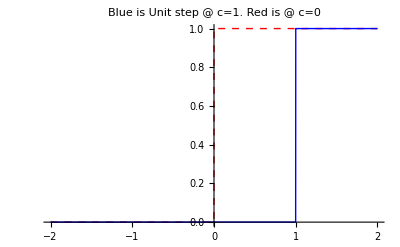

```mathematica
Plot[{HeavisideTheta[t], HeavisideTheta[t-1]},{t,-2,2},PlotStyle->{{Thick,Dashed,Red},{Thick,Blue}},PlotLabel->"Blue is Unit step @ c=1. Red is @ c=0"]
```

Often we care not just about f(t) but about u_c(t) * f(t-c) we will show the difference between the two in the set of graphics below. In the second plot we have the exact same equation, but this time it is shifted 2 to the right:

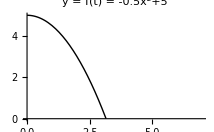
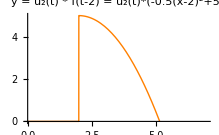

```mathematica
plot1 =Plot[-1/2x^2+5,{x,0,7},PlotRange->{0,5},PlotStyle->Black,PlotLabel->"y = f(t) = -0.5x^2+5"];
plot2 =Plot[HeavisideTheta[x-2]*(-1/2(x-2)^2+5),{x,0,7},PlotRange->{0,5},PlotStyle->Orange,PlotLabel->"y = u_2(t) * f(t-2) = u_2(t)*(-0.5(x-2)^2+5)"];
{plot1,plot2}
```

### The first Shifting Theorem

ℒ{u_c(t)f(t-c)} = e^-cs ℒ{f(t)} = e^-cs F(s)

Equation (6.4) is the result of what is known as “the first shifting theorem”

This means that the translation of f(t) by a distance c in the positive t direction (created by f(t-c) ) corresponds to the multiplication of F(s) by e^-cs. (translation → multiplication).

### Examples of Laplace Transforms of Step Functions

-Graphics-

### The Second Shifting Theorem

If F(s)  = ℒ{f(t)} exists for s>a≥0, and if c is a constant, then

L{e^ct f(t)} = F(s-c)

This means that the multiplication of f(t) by e^ct resuilts in a translation of the transform F(s) a distance c in teh positive s direction (created by F(s-c) ). (multiplication → translation)

### Examples of the second Shifting Theorem

-Graphics-

### Using the shifting theorems to find the Laplace transform of products

In order to apply the first shifting theorem you will need to make sure you have u_cf(t-c) and the c’s are the same. To do this you might have to break somethings up in the f(t-stuff) function. This is shown below:

Solve for Y = L{y} for y''+49y = {2t | 0≤t<6
14 | t>6 = u_0(t)*2t - u_6(t) *(2t-14)

(s^2+49)L{y} = L{2t} - ℒ{2*u_6(t) *(12-7)} = 2/s^2 - ℒ{2*u_6(t) *(12-6-1)} = 2/s^2 - 2*(ℒ{u_6(t) *(12-6)}-ℒ{u_6(t)*1})

= 2/s^2- 2(e^(-6s)/s^2-e^(-6s)/s)

## 6.4: Differential Equations with Discontinuous Forcing Functions

We will now look at cases where the non-homogeneous term, or forcing function, is discontinuous.

### Steps to solving Linear ODE’s with discontinuous forcing functions

Take the Laplace Transform of the differential equation.

Factor the left hand side and solve for ℒ{y} (Y).

Separate the right side of the equation into the exponential terms (that come from Heaviside function) and the others and name the other stuff H(s). You will have a product of exponentials and a common H(s).

Do a partial fraction decomposition on H(s) to be able to take the inverse Laplace transform of the exponential H(s) product.

### Example

-Graphics-
-Graphics-
-Graphics-=
-Graphics-
-Graphics-
-Graphics-

## 6.5: Impulse Functions

Sometimes in physical problems you have impulse forces, or forces that only act for a short amount of time but are large in magnitude.

There is a function called the dirac delta function that has total impulse of 1, but acts for an infinitely small period of time. (impulse is integral of force with respect to time).

∫_(-∞)^∞ δ(t-t_0)dt=1

The above equation (6.6) is the definition of the dirac delta function at time t_0.

ℒ{δ(t-c)} = e^-cs

If the forcing function is the sum of multiple impulse functions, the Laplace of is is just the sum of the individual Laplaces.

If your forcing function is a large (even infinite) sum, keep the Laplace in summation notation as follows:

ℒ{∑_(n=1)^k δ(t-n)} = ∑_(n=1)^k e^-ns

### Steps for solving ODE’s with impulsive forcing functions

Take the Laplace of both side of the function and solve for ℒ{y}.

Separate the right side into the exponential terms and other stuff we will call H(s)

Find the inverse Laplace Transform of H(s) (h(t)).

Multiply h(t) by u_c and change the “t” in h(t) to (t-c)

## 6.6: The Convolution Integral

We now look at the Laplace Transform of the product of two general functions. It is not true that multiplication in our world leads to multiplication in the Laplace world, but there is a connection.

Let F(s) = ℒ{f(t)} , G(s) = ℒ{g(t)}, and H(s) = F(s)G(s), then

h(t) = ∫_o^t f(t-τ)g(t)dτ = ∫_0^t f(τ)g(t-τ)dτ

Equation (6.8) is known as the convolution integral and is the definition of the Laplace transform of a product.

It is also expressed as h(t) = f⋆g = g⋆f.

### Properties of the Convolution Integral

The Convolution integral (CI) obeys the commutitive law:  f⋆g = g⋆f

The CI obeys the distributive law: f⋆(g_1+g_2) = f⋆g_1+f⋆g_2.

The CI obeys the associative law: (f⋆g)⋆h = f⋆(g⋆h)

The convolution of a function and zero is zero: f⋆0  =  0⋆f  = 0

The convolution of f and 1 is not f: f⋆1≠f.

The convolution of f and the dirac Delta function (δ) is f: (f⋆ δ)(t) = f(t)

### Examples

-Graphics-

-Graphics-

7

Systems of First  Order Linear Equations

## 7.1: Introduction

There are many physical systems in which two or more components are linked in a way that they both vary according to the same variables. These are systems of differential equations that must be solved at the same time.

We wil borrow heavily from Linear Algebra principles in displaying and solving these systems.

Some common examples of systems of differnetial equaitons are multiple mass spring systems, paralell LRC circuits, and the two tank mixing problem

A higher order equation can almost always be transformed into a system of first order equations. This is usually done by starting with an equation of the form :

u''+ αu' = βu = 0

And  then saying x_1 = u, x_2 = u' which leads to x_1' = x_2 and u'' = x_2'. You can then rewrite (7.1) as a system of first order equations in this way:

x_1' = x_2,  x_2' = -α x_2 - β x_1

### The two tank mixing problem.

-Graphics-

-Graphics-

-Graphics-

## 7.2: Review of Matricies

See Linear Algebra Review.

## 7.3: Linaer Algebreic Equations; Linear Independence, Eigenvalues, Eigenvectors

See Linear Algebra Review

To make life easier, remember that the eigenvalues of any triangular matrix are the entries on the main diagonal.

## 7.4: Basic Theory of Systems of First Order Linear Differential Equations

The theory behind a system of first order linear ODE’s is not that different from a single one. You have a basic form x’ = P(t)x + g(t), but instaed of being scalars or single functions; x’, x, P(t), g(t) are all vectors or vector functions.

The form of a homogeneous system of equations is :

x' = P(t)x

Just like before, once we have solved the homogenous equation, it is relatively easy to get the general solution. We simply find one particular solution and then add it to the homogeneous one.

Also, as before, if the entries of P(t)  and the components of g(t) are continuous on an open interval I containing t_0, then there is a unique solutio to the IVP on that interval.

If all the solutions we find are linearly independent (check with the wronskian), then they form a fundamental set and are therefore a general solution to that system.

To find the wronskian of a set of solution vectors you simply express them as column vectors and make them into a matrix, one column vector at a time. Once that matrix is constructed you just take its determinant and that is the wronskian.

## 7.5: Homogeneous Linear Systems with Constant Coefficients

Phase Plane: The phase plane is a diagram depicting the the solutions to a system of two equations. The drawing is in the x_1,x_2 plane (those are the two solutions) and small arrows are drawn that represent the tangent vector at each point. Very similar to before.

Phase Portrait: A phase portrait is very similar, except you have the phase plane with some sample solution trajectories drawn also.

### Steps to solving a system of 2 (just for simplicity, principles extend to higher numbers) linear ODE’s with constant coefficients.

Express your system of equations in a matrix that looks like this: (x_1'(t)
x_2'(t)) = A (x_1(t)
x_2(t)) = (a_11 | a_12
a_21 | a_22) (x_1(t)
x_2(t)), where all the a’s are scalars.

Find the eigenvalues (λ) for the matrix A

Find the eigenvectors (ξ) associated with those eigenvalues.

Construct solutions of the form x_1 = ξ_1 e^(λ_1 t) and x_2 = ξ_2 e^(λ_2 t) .

Verify solutions by taking derivatives and multipliying by A.

If you follow the steps above there are three possibilities for the eigenvalue pairs:

They are real and distinct.

They are complex conjugate solutions,

They are real repeated roots.

If you get situation a above the solutions are constructed by following step 4 and they will, by definition, be linearly independent and a fundamental set.

Situation b is addressed in section 7.6 and situation d is addressed in section 7.8.

## 7.6: Complex Eigenvalues

We are again talking about a system of n linear homogeneous equations with constant coefficients: x’ = A x

If we find the eigenvalues and see that they are complex they will ALWAYS be in complex conjugate pairs. It turns out that the eigenvectors associated with that pair are also ALWAYS complex conjugate pairs and we only need to solve for one of them.

### Steps to solving a system with complex eigenvalues

Express the system in this form: (x_1'(t)
x_2'(t)) = A (x_1(t)
x_2(t)) = (a_11 | a_12
a_21 | a_22) (x_1(t)
x_2(t))

Find the complex eigenvalues of A (λ ± ι μ)

Find an eigenvector (ξ_1 = a_1 + ι b_1) for one of those eigenvalues and split it into its imaginary and real parts.

Take the eigenvector with a positive complex part and use this formula:

u(t) =e^(λ_1 t) * {a_1 Cos[μ_1 t] - b_1 Sin[μ_1 t]}
v(t) =e^(λ_1 t) * {a_1 Sin[μ_1 t] + b_2 Cos[μ_1 t]}

Form the general solution to the system by saying x(t) = c_1 u(t) + c_2 v(t)

In the steps above, note that we are only using one eigenvector. We never even solve for the other one.

### Example of Complex Eigenvalues

-Graphics-

## 7.7: Fundamental Matricies

Sometimes it is useful to express solutions to systems of ODE’s in the form of a matrix. Instead of writing that x = c_1 x^(1)+...+c_n x^(n) you can simply write x = Ψ(t)c

The matrix Ψ is called a fundamental matrix and it is constructed by taking the vector solutions of the system and making them be the columns of Ψ. Because of how the columns of Ψ are formed, the matrix is non-singular.

### Example of Constructing Ψ

Assume you have a system with solutions x_1 = (e^(2t)
3 e^t) and x_2 = (2 e^(2t)
e^t), then Ψ(t) = (e^(2t) | 2 e^(2t)
3 e^t | e^t)

We usually express the intitial conditions for and IVP in this way x(t_0) = x^0. This makes the fundamental matrix representation of the IVP solution Ψ(t_0) c = x^0.

Solving the above expression we get c = Ψ^-1(t_0)  x^0 → x = Ψ(t) Ψ^-1(t_0) x^0.

There is another fundamental matrix Φ  which is equal to:

Φ = Ψ(t)  Ψ^-1(t_0)

## 7.8: Repeated Eigenvalues

The third and final possibility for eigenvalues is that they are real and repeated.

This could pose problems becuase often you will not get a set of two linearly independent eigenvectors (it is possibile, but rare).

In the past when we had repeated roots we made a guess that we had e^rt and then t e^rt. While that won’t quite work anymore, we will do something silmilar in this case.

### Steps to solving repeated eigenvalues case

Express your system of equations in a matrix that looks like this: (x_1'(t)
x_2'(t)) = A (x_1(t)
x_2(t)) = (a_11 | a_12
a_21 | a_22) (x_1(t)
x_2(t)),

Find the repeated, real eigenvalue (λ) of A.

Find 1 or 2 linearly independent eigenvectors (ξ) for the eigenvalue (λ)

If there was only one, find a generalized eigenvector (η) by taking the matrix (A - λI) and augmenting it with the real eigenvector (ξ). The perform row operations until you can create another eigenvalue (η).

Construct the solution in this way:

x = x^(1)+x^(2) = (ξ e^λt) + ξ t e^λt+η e^λt,where x^(2) = ξt e^λt+η e^λt

## 7.9: Nonhomogeneous Linear Systems

The Theory behind this section is very similar to what we have already seen. We will first solve the corresponding homogeneous system and then find a single particular solution and add it to the homogeneous.

### Steps to solving non-homogeneous system

Solve the corresponding homogeneous case

Construct the fundamental matrix Ψ(t).

Use Ψ(t) to find Φ(t). (remember not to evaluate Φ at t=0)!

Construct a particular solution in this way, ν(t) = Ψ(t) ∫_0^t Ψ^-1(τ)*g(τ)ⅆτ

Contruct the general solution by adding the particular to the homogeneous.

### Example

-Graphics-

-Graphics-

## Extra: Stability, Direction, and Appearance

### Real, Distinct Eigenvalues

#### r1 > r2 > 0

Unstable node

-Graphics-

#### r1 < r2 < 0

Asomptotically Stable node

-Graphics-

#### r2 < 0 < r1

Unstable Saddle Point

-Graphics-

### Compex Eigenvalues

#### r = λ ± ι μ with λ > 0

Unstable spiral point

-Graphics-

#### r = λ ± ι μ , λ < 0

Asomptotically Stable Spiral Point

-Graphics-

#### r = ± ι μ

Stable Center Point

-Graphics-

### Real, Repeated Eigenvalues

#### r1=r2 > (<) 0, proper node

Unstable (asomptotically stable) proper node.

-Graphics-

#### r1=r2 > (<) 0, improper node

Unstable (asomptotically stable) improper node.

-Graphics-

8

9

Nonlinear Differential Equations and Stability

## 9.1: The Phase Plane: Linear Systems

There are a lot of differential equations that can’t be solved analytically. In these cases it is often very instructive to contruct a picture of what the solutions are doing. This is done using a phase plane.

We have discussed this idea already and given great examples of what it looks like so we will skip it here.

## 9.2: Autonomous Systems and Stability

Autonomous Systems: These are systems of two or more differential equaitons with the same explanatory variables, but that don’t depend on the variable t as defined in the next sentence.  We are concerned aoub tsystems of two simultaneous differential equations of the form dx/dt = F(x,y) and dy/dt = G(x,y)

If the functions F(x,y) and G(x,y) are continuous on an open interval in the xy plane, then there is a unique solution to the IVP defined by x(t_0) = x_0 and y(t_0) = y_0.

Critical Points: A point is said to be a critical point if it is not moving in time. We know this is true because dx/dt and dy/dt are simultaneously zero.

Stable: A critical point is stable if, given any ϵ >0, there is a δ > 0 such that if you start within δ the solution never leaves ϵ.

Asomptotically Stable: A critical point is said to be asomptotically stable if inside a certain δ_0the solution converges to the critical point.

Basin of Attraction: For all asomptotically stable critical points, there is something called a basin of attraction in which all solution curves that start inside the region will converge to the critical point.

Separtrice: A separtrice is a solution curve that separates one basin of attraction from another.

Sometimes you can find what some solution curves look like in the xy plane by computing dy/dx from dx/dt and dy/dt using the chain rule in this way:

dy/dx = (dy/dt)/(dx/dt) = (G(x,y))/(F(x.y))

Using (9.1) it might be possible to construct some trajectories of the solution in the form H(x,y) = C

### Example of finding trajectories

-Graphics-

### Finding the critical points

To find the critical points you will want to factor dx/dt and dy/dt as much as possible and then set one factor from each equal to zero at the same time and solve little linear systems.

#### Example

-Graphics-

## 9.3: Locally Linear Systems

After finding the critical points we can treat them as isolated systems and get a better idea about how they look.

### Steps to fiding local linearizations

Find all critical points

Find first order partials of F and G with repsect to x and y

Construct a matrix A = (F_x(x_0,y_0) | F_y(x_0,y_0)
G_x(x_0,y_0) | G_y(x_0,y_0)), where (x_0,y_0) is a critial point. You now have a locally linear system u’ = A u. A is called the Jacobian matrix.

Find the eigenvalues (λ) and eigenvectors (ξ) for the locally linear system.

Determine the stability and shape of the systems by evaluating the eigenvalues.

Repeat steps 3-5 for all critical points.

## 9.4: Competing Species

This is pretty much the same thing as the last section, just with a real world bilogical application.

## 9.5: Predator-Prey Equaiotns

Again, pretty much the same steps as above.  In this case we do have to follow a few assumptions:

If there is no predator, the prey will grow according to the current population.

If there is no prey, the predator will die out.

Teh number of encounters between predator and prety depend on their total popualtion sizes.

## 9.6: Liapunov’s Second Method

One of these is on the test.

The main way to think about this is that you have to redifine the way you measure distance before you can define stability.

-Graphics-